## Configuration

```mathematica
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];

(* 
This notebook tries to calculate the order(alpha_s tau) thrust rate in SCET. 
*)
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

Loading FeynCalc from /Users/Matt/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

Notebook load complete.

```mathematica
$LimitTo4//myPrint
turnOffConditional[];
```

$LimitTo4=False

```mathematica
loadDefaultAssumptions[]
$Assumptions
```

$Assumptions=0<ϵ<1/10∧-1/10<ϵ^-<0∧0<0^+<1/10∧M>0∧Q>0∧p_1^->0∧p_1^+>0∧p_2^+>0∧p_2^->0∧0<η<1/10

0<ϵ<1/10∧-1/10<ϵ^-<0∧0<0^+<1/10∧M>0∧Q>0∧p_1^->0∧p_1^+>0∧p_2^+>0∧p_2^->0∧0<η<1/10

```mathematica
$Assumptions=0<tau<1/3&&0<qhatp<1&&0<qhatm<1;

replSingVarPlus[e_]:=e/.PlusDistribution[a_*HeavisideTheta[b_]]:>HeavisideTheta[b-beta]a+DiracDelta[b-beta]Integrate[a,{tau,1,tau}];
expLogs[e_]:=e//.Log[a_/b_]:>Log[a]-Log[b]//.Log[a_*b_]:>Log[a]+Log[b]/.Log[a_^n_]:>  n*Log[a];

nondimensionalize[e_]:=e/.qm->qhatm*Q/.qp->qhatp*Q/.p1m->p1hatm*Q/.p1p->p1hatp*Q/.p2m->p2hatm*Q/.p2p->p2hatp*Q/.Vperp[p1]->Vperp[p1hat]*Q/.Vperp[p2]->Vperp[p2hat]*Q;
dimensionalize[e_]:=e/.qhatm->qm/Q/.qhatp->qp/Q/.p1hatm->p1m/Q/.p1hatp->p1p/Q/.p2hatm->p2m/Q/.p2hatp->p2p/Q;

(* 2 body kinematics for Vperp[k]=0 *)
kinematics2Body[e_]:=nondimensionalize[e]/.p1hatm->1/.p1hatp->0/.p2hatm->0/.p2hatp->1/.Vperp[p1hat]->0/.Vperp[p2hat]->0;

(* 3 body kinematics *)
varx=x23;
kinematics3Body[e_]:=nondimensionalize[e]/.Vperp[p1hat]->-Vperp[qhat]/.p2hatm->0/.p2hatp->1-qhatp-p1hatp/.p1hatp->qhatp*qhatm/p1hatm/.p1hatm->1-qhatm/.qhatp->x13*(1-qhatm)/.qhatm->x23/(1-x13);
If[varx==qhatm,
kinematics3Body[e_]:=nondimensionalize[e]/.Vperp[p1hat]->-Vperp[qhat]/.p2hatm->0/.p2hatp->1-qhatp-p1hatp/.p1hatp->qhatp*qhatm/p1hatm/.p1hatm->1-qhatm/.qhatp->x13*(1-qhatm)/.qhatm->x23/(1-x13)/.x23->qhatm*(1-x13);
];

(* the following from Collins A.43 and A.44 *)
phaseSpace2Dprefac=(Q^2/(16*Pi))^((D-4)/2)/(16*Sqrt[Pi]*Gamma[(D-1)/2])/.D->4-2*eps;
phaseSpace3Dprefac=(Q^2/(16*Pi))^((D-2)/2)*( Q^2/(4Pi))^(-eps)/(16*Sqrt[Pi]*Pi*Gamma[(D-1)/2]*Gamma[(D-2)/2])/.D->4-2*eps//Simplify
phaseSpace3Dprefac=(Q^2/(16*Pi^2))^((D-2)/2)*( Q^2/(4))^(-eps)/(16*Sqrt[Pi]*Gamma[(D-1)/2]*Gamma[(D-2)/2])/.D->4-2*eps//Simplify

Unprotect[Tr];
Tr/:Tr[0]:=0;
Protect[Tr];

c2=1+(alphabar/2)(-2/eps^2+(2Log[(-Q^2-I*delta)/muMS^2]-3)/eps-Log[(-Q^2-I*delta)/muMS^2]^2+3*Log[(-Q^2-I*delta)/muMS^2]+Pi^2/6-8);
(* below is the correction to the tree level amplitude squared due to virtual corrections *)
kFactor=((Series[c2*ComplexConjugate[c2],{alphabar,0,1}]//Normal//expLogs)/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi//Simplify)/.Pi^2->zeta2*6//Expand;

spinSumHornig0g=-(MTD[mu,nu]-FVD[n+nb,mu]FVD[n+nb,nu]/4);
spinSumHornig=(-MTD[alpha,beta])(-(MTD[mu,nu]-FVD[n+nb,mu]FVD[n+nb,nu]/4));

spinSum0g=spinSumHornig0g;
spinSum=spinSumHornig;
```

(4^(3 ϵ-4) π^(2 ϵ-5/2) (Q^2)^(1-2 ϵ))/(1-ϵ 3/2-ϵ)

(4^(3 ϵ-4) π^(2 ϵ-5/2) (Q^2)^(1-2 ϵ))/(1-ϵ 3/2-ϵ)

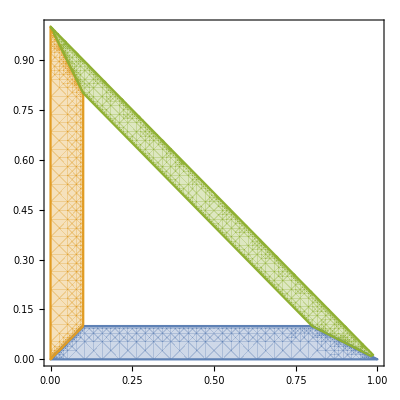

```mathematica
regA=x13<tau&&x13<x23&&x13<x12&&x13>0&&x23>0&&x12>0;
regB=x23<tau&&x23<x13&&x23<x12&&x13>0&&x23>0&&x12>0;
regC=x12<tau&&x12<x13&&x12<x23&&x13>0&&x23>0&&x12>0;
plotPS={regA,regB,regC}/.tau->0.1/.x12->1-x13-x23//kinematics3Body;
RegionPlot[plotPS,{x23,0,1},{x13,0,1},MaxRecursion->5]
```

## Integral Tables in Dalitz Space

```mathematica
(* we divide the integration into four disjoint regions  *)

(* Region A -- blue   -- the region where p2 has the largest energy  *)
(* Region B -- orange -- the region where p1 has the largest energy  *)
(* Region C -- green  -- the region where q has the largest energy   *)
(* Region τ -- white  -- the region where the thrust τ=1-T is larger than some value τ *)
(*
-Graphics-
(* ^Here the x-axis is x23 and the y-axis is x13 *)
*)

measure=(x13*x23*(1-x13-x23))^(eps);  (* The transformed measure from Collins FoPQCD eq. A44  *)
commonDenominator=x13*x23; 

(* the denominator that appears when we combine amplitudes squared *)
```

### Phase Space Integrals

#### A -- Sideways Integration (x-first)

```mathematica
regAs1=Integrate[x^(n-1+eps)(1-x-y)^(eps),{x,y,1-2*y},Assumptions->0<y<1/3]//Normal;
```

```mathematica
Series[regAs1*y^(m-1+eps)/.n->3/.m->0,{y,0,2},Assumptions->0<y<1/3]//Normal
regAs2=Integrate[%,{y,0,tau}];
regAs3=Series[%,{tau,0,2}]//Normal;
Series[%,{eps,0,0},Assumptions->0<eps<1/10]//Normal;
Series[%,{tau,0,1}]//Normal//FullSimplify
Series[%,{eps,0,0}]//Normal//FullSimplify;
```

y^(ϵ-1) (((3 π y^2 (ϵ+2) csc(π (ϵ+1)))/(-ϵ ϵ+3)-(3 π y^3 csc(π (ϵ+1)) (2 ϵ+2 ϵ^2+4 ϵ+2 ϵ-ϵ+3 ϵ-ϵ+3))/(-ϵ ϵ+2 ϵ+3)) y^ϵ+((π y^2 ϵ (ϵ+2) csc(π (ϵ+1)))/(-ϵ ϵ+3)-(π y^3 ϵ csc(π (ϵ+1)) (2 ϵ+2 ϵ^2+4 ϵ+2 ϵ-ϵ+3 ϵ-ϵ+3))/(-ϵ ϵ+2 ϵ+3)) y^ϵ+((π y^2 csc(π (ϵ+1)) (2 ϵ+2 ϵ^2+5 ϵ+2 ϵ-ϵ+3 ϵ+2 ϵ+2-ϵ+3))/(-ϵ ϵ+2 ϵ+3)-(π y (ϵ+2) csc(π (ϵ+1)))/(-ϵ ϵ+3)) y^ϵ-(π ϵ^2 (ϵ+2) csc(π (ϵ+1)) y^(ϵ+3))/(2 -ϵ ϵ+3)-(5 π ϵ (ϵ+2) csc(π (ϵ+1)) y^(ϵ+3))/(2 -ϵ ϵ+3)-(3 π (ϵ+2) csc(π (ϵ+1)) y^(ϵ+3))/(-ϵ ϵ+3)+((π (2 ϵ^2+5 ϵ+3) csc(π (ϵ+1)) ϵ+4)/((ϵ+3) -ϵ 2 ϵ+4)+((-2 ϵ-3) (-π csc(π (ϵ+1)) 1-ϵ ϵ+4-π ϵ csc(π (ϵ+1)) -ϵ ϵ+4))/(1-ϵ -ϵ 2 ϵ+4)+(π csc(π (ϵ+1)) 1-ϵ -ϵ ϵ+4 ϵ^3+3 π csc(π (ϵ+1)) 1-ϵ -ϵ ϵ+4 ϵ^2+2 π csc(π (ϵ+1)) 2-ϵ -ϵ ϵ+4 ϵ^2+π csc(π (ϵ+1)) 1-ϵ 2-ϵ ϵ+4 ϵ-4 π csc(π (ϵ+1)) 1-ϵ -ϵ ϵ+4 ϵ+4 π csc(π (ϵ+1)) 2-ϵ -ϵ ϵ+4 ϵ)/(2 1-ϵ 2-ϵ -ϵ 2 ϵ+4)) y^2+((π (-2 ϵ-3) csc(π (ϵ+1)) ϵ+4)/((ϵ+3) -ϵ 2 ϵ+4)+(-π csc(π (ϵ+1)) 1-ϵ ϵ+4-π ϵ csc(π (ϵ+1)) -ϵ ϵ+4)/(1-ϵ -ϵ 2 ϵ+4)) y+(π csc(π (ϵ+1)) ϵ+4)/((ϵ+3) -ϵ 2 ϵ+4))

Piecewise[{{1/8 τ^ϵ ((π^(3/2) 4^-ϵ (2 τ ϵ^2+(3 τ-1) ϵ-1) csc(π ϵ))/(ϵ (ϵ+1)^2 -ϵ-2 ϵ+5/2)+(τ ((π τ 4^-ϵ csc(π ϵ) (2^(2 ϵ+3) ϵ^2 ϵ+5/2 ϵ+4+√π (-2 ϵ^3-3 ϵ^2+2 ϵ+3) 2 ϵ+5))/((ϵ-1) -ϵ ϵ+5/2)-(4 (2 π τ ϵ^3 (ϵ+1)^2 (4 ϵ^2+8 ϵ+3) csc(π ϵ) ϵ+4+(-9 τ+6 τ^2 ϵ^4+τ (27 τ-8) ϵ^3+(30 τ^2-28 τ+4) ϵ^2+(9 τ^2-30 τ+10) ϵ+6) τ^ϵ 2-ϵ 2 ϵ+5))/((ϵ+1)^2 (2 ϵ+1) (2 ϵ+3) 2-ϵ)))/(2 ϵ+5)), Re(ϵ)>0}, {0, True}}]

Piecewise[{{-1/(2 (ϵ+1)^2 (2 ϵ+1) (2 ϵ+3))τ^ϵ (4 ϵ^2 τ^(ϵ+1)+10 ϵ τ^(ϵ+1)+6 τ^(ϵ+1)-8 ϵ^3 τ^(ϵ+2)-28 ϵ^2 τ^(ϵ+2)-30 ϵ τ^(ϵ+2)-9 τ^(ϵ+2)+6 ϵ^4 τ^(ϵ+3)+27 ϵ^3 τ^(ϵ+3)+30 ϵ^2 τ^(ϵ+3)+9 ϵ τ^(ϵ+3)+(-1/((ϵ-1) (ϵ+1)^2 (2 ϵ+1) (2 ϵ+3) -ϵ-2 2-ϵ -ϵ ϵ+5/2 2 ϵ+5)2^(-2 ϵ) (-2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^9-3 2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^8-8 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^8+2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^7-7 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^7-44 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^7+2^(2 ϵ+7) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^6+9 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^6-86 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^6+23 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^5+11 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^5-53 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^5+7 2^(2 ϵ+4) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^4+3 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^4+46 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^4+3 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^3+88 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^3+48 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^2+9 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ) ϵ^3-1/((ϵ-1) (ϵ+1)^2 (2 ϵ+1) (2 ϵ+3) -ϵ-2 2-ϵ -ϵ ϵ+5/2 2 ϵ+5)2^(2-2 ϵ) (-2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^9-3 2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^8-8 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^8+2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^7-7 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^7-44 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^7+2^(2 ϵ+7) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^6+9 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^6-86 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^6+23 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^5+11 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^5-53 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^5+7 2^(2 ϵ+4) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^4+3 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^4+46 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^4+3 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^3+88 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^3+48 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^2+9 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ) ϵ^2-1/((ϵ-1) (ϵ+1)^2 (2 ϵ+1) (2 ϵ+3) -ϵ-2 2-ϵ -ϵ ϵ+5/2 2 ϵ+5)23 2^(-2 ϵ-2) (-2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^9-3 2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^8-8 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^8+2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^7-7 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^7-44 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^7+2^(2 ϵ+7) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^6+9 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^6-86 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^6+23 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^5+11 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^5-53 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^5+7 2^(2 ϵ+4) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^4+3 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^4+46 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^4+3 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^3+88 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^3+48 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^2+9 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ) ϵ-1/((ϵ-1) (ϵ+1)^2 (2 ϵ+1) (2 ϵ+3) -ϵ-2 2-ϵ -ϵ ϵ+5/2 2 ϵ+5)7 2^(-2 ϵ-1) (-2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^9-3 2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^8-8 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^8+2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^7-7 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^7-44 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^7+2^(2 ϵ+7) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^6+9 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^6-86 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^6+23 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^5+11 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^5-53 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^5+7 2^(2 ϵ+4) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^4+3 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^4+46 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^4+3 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^3+88 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^3+48 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^2+9 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ)-1/((ϵ-1) (ϵ+1)^2 (2 ϵ+1) (2 ϵ+3) -ϵ-2 2-ϵ -ϵ ϵ+5/2 2 ϵ+5 ϵ)3 2^(-2 ϵ-2) (-2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^9-3 2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^8-8 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^8+2^(2 ϵ+5) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^7-7 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^7-44 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^7+2^(2 ϵ+7) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^6+9 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^6-86 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^6+23 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^5+11 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^5-53 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^5+7 2^(2 ϵ+4) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^4+3 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 -ϵ ϵ+5/2 ϵ+4 ϵ^4+46 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^4+3 2^(2 ϵ+3) π csc(π ϵ) -ϵ-2 2-ϵ ϵ+5/2 ϵ+4 ϵ^3+88 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^3+48 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ^2+9 π^(3/2) csc(π ϵ) -ϵ-2 2-ϵ 2 ϵ+5 ϵ)) τ^2-(2^(-2 ϵ-2) π^(3/2) (2 ϵ+1) (2 ϵ+3)^2 csc(π ϵ) τ)/(-ϵ-2 ϵ+5/2)+(2^(-2 ϵ-2) π^(3/2) (ϵ+1) (4 ϵ^2+8 ϵ+3) csc(π ϵ))/(ϵ -ϵ-2 ϵ+5/2)), Re(ϵ)>0}, {0, True}}]

1/6 (12 τ^2-12 τ+2 log(τ)-2 ℽ+1-4 log(2)-2 05/2)+1/(3 ϵ)

1/18 (-36 τ+6 log(τ)+6/ϵ-13)

1/18 (-36 τ+6 log(τ)+6/ϵ-13)

```mathematica
(* try integrating x first, then y *)

(*
regAs1=Integrate[x^(n-1+eps)(1-x-y)^(eps),{x,y,1-2*y}];
regAs2=Integrate[%*y^(m-1+eps),{y,0,tau}];
regAs3=Series[%,{tau,0,2}]//Normal;
*)

(* it worked but the output is HUGE! Almost 57000 terms long *)

(* instead of keeping the huge result, we'll store the 4x4 {n,m} elements that are necessary for usual calculations *)
(* remember, the epsilons here are IR regulators, so negative. Later, use /.eps->negeps/.negeps->-eps to revert back to regular epsilons *)

regA00=-Pi^2/6+1/(2*ϵ^2)-2*τ-Log[τ]^2/2; 
regA01=τ*(1-Log[τ]);
regA02=0;
regA03=0;

regA10=-2+ϵ^(-1)-3*τ+Log[τ];
regA11=τ;
regA12=0;
regA13=0;

regA20=-1+1/(2*ϵ)-2*τ+Log[τ]/2;
regA21=τ/2;
regA22=0;
regA23=0;
1/18 (-36 τ+6 log(τ)+6/ϵ-13)
regA30=-13/18+1/(3*ϵ)-2*τ+Log[τ]/3;
regA31=τ/3;
regA32=0;
regA33=0;

intTotalA[n_,m_]:=Switch[{n,m},{0,0},regA00 ,{0,1},regA01,{0,2},regA02,{0,3},regA03,{0,4},regA04,
							    {1,0},regA10 ,{1,1},regA11,{1,2},regA12,{1,3},regA13,{1,4},regA14,
						   	 {2,0},regA20 ,{2,1},regA21,{2,2},regA22,{2,3},regA23,{2,4},regA24,
						    	{3,0},regA30 ,{3,1},regA31,{3,2},regA32,{3,3},regA33,{3,4},regA34,
						    	{4,0},regA40 ,{4,1},regA41,{4,2},regA42,{4,3},regA43,{4,4},regA44]/.eps->-eps;
```

```mathematica
(*
Integrate[x^(0-1+eps)(1-x-y)^(eps),{x,y,1-2*y}]
Integrate[%*y^(0-1+eps),{y,0,tau}]
Series[%,{tau,0,4}]//Normal

Series[%,{tau,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%,{tau,0,1}]//Normal
*)
```

#### B -- Vertical Integration (y-first)

```mathematica
(* summary *)

regB00=regA00;
regB01=regA10;
regB02=regA20;
regB03=regA30;

regB10=regA01;
regB11=regA11;
regB12=regA21;
regB13=regA31;

regB20=regA02;
regB21=regA12;
regB22=regA22;
regB23=regA32;

regB30=regA03;
regB31=regA13;
regB32=regA23;
regB33=regA33;
```

```mathematica
(*
Integrate[y^(m-1+eps)(1-x-y)^(eps),{y,x,1-2*x}]
Integrate[%*x^(n-1+eps),{x,0,tau}]
regBlong=Series[%,{tau,0,2}]//Normal
*)

(* this is equivalent to the region A integration, but with n interchanged with m *)
```

#### C -- Sideways Integration (x-first)

```mathematica
(* summary *)

(* it looks like I only need to know the result for c02, c11, and c20, so let's just do those *)

(* remember, the epsilons here are IR regulators, so negative. Later, use /.eps->negeps/.negeps->-eps to revert back to regular epsilons *)

regC00=τ*(2-2*Log[τ]);
regC01=τ-τ*Log[τ];
regC02=-(τ*Log[τ]);
regC03=τ*(-1/2-Log[τ]);

regC10=τ*(1-Log[τ]);
regC11=τ;
regC12=τ/2;
regC13=τ/3;

regC20=-(τ*Log[τ]);
regC21=τ/2;
regC22=τ/6;
regC23=τ/12;

regC30=-(τ*(1+2*Log[τ]))/2;
regC31=τ/3;
regC32=τ/12;
regC33=τ/30;

intC[n_,m_]:=Switch[{n,m},{0,0},regC00 ,{0,1},regC01,{0,2},regC02,{0,3},regC03,{0,4},regC04,
							    {1,0},regC10 ,{1,1},regC11,{1,2},regC12,{1,3},regC13,{1,4},regC14,
						   	 {2,0},regC20 ,{2,1},regC21,{2,2},regC22,{2,3},regC23,{2,4},regC24,
						    	{3,0},regC30 ,{3,1},regC31,{3,2},regC32,{3,3},regC33,{3,4},regC34,
						    	{4,0},regC40 ,{4,1},regC41,{4,2},regC42,{4,3},regC43,{4,4},regC44]/.eps->-eps;
```

```mathematica
(* convert integrals from y to u=1-x-y *)
(* then the integration region has the same form as region A so we can try the sideways integration again *)

(*nn=1;
mm=1;

regCs02i=Integrate[x^(nn-1+eps)(1-x-u)^(mm-1+eps),{x,u,1-2*u}]

%/.Hypergeometric2F1Regularized[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1Regularized[a,b,c,d],eps,2]/.Hypergeometric2F1[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1[a,b,c,d],eps,2]/.Beta[z_,a_,b_]:>(z^a/a)*HypExp[Hypergeometric2F1[a,1-b,1+a,z],eps,2]

regCs02ii=Integrate[%*u^eps,{u,0,tau}]
regCs02=Series[%,{tau,0,2}];
regCs02=Series[%,{tau,0,1}]//Normal;
regCs02=Series[%,{eps,0,0}]//Normal
regCsnnmm=Series[%,{tau,0,1}]//Normal
regCsnnmm//InputForm*)
```

#### Overall

```mathematica
int00=regA00+regB00+regC00;
int01=regA01+regB01+regC01;
int02=regA02+regB02+regC02;
int03=regA03+regB03+regC03;

int10=regA10+regB10+regC10;
int11=regA11+regB11+regC11;
int12=regA12+regB12+regC12;
int13=regA13+regB13+regC13;

int20=regA20+regB20+regC20;
int21=regA21+regB21+regC21;
int22=regA22+regB22+regC22;
int23=regA23+regB23+regC23;

int30=regA30+regB30+regC30;
int31=regA31+regB31+regC31;
int32=regA32+regB32+regC32;
int33=regA33+regB33+regC33;

intTotal[n_,m_]:=Switch[{n,m},{0,0},int00 ,{0,1},int01,{0,2},int02,{0,3},int03,{0,4},int04,
							    {1,0},int10 ,{1,1},int11,{1,2},int12,{1,3},int13,{1,4},int14,
						   	 {2,0},int20 ,{2,1},int21,{2,2},int22,{2,3},int23,{2,4},int24,
						    	{3,0},int30 ,{3,1},int31,{3,2},int32,{3,3},int33,{3,4},int34,
						    	{4,0},int40 ,{4,1},int41,{4,2},int42,{4,3},int43,{4,4},int44]/.eps->-eps;
```

## Rate Calculation SCET 0 gluons

### < O_2 | O_2 >

```mathematica
(* leading order vector amplitude *)
ampSCET0g=I*SpinorUBar[p1].Phatnb.GAD[mu].Phatnb.SpinorV[p2];
ampSCET0gDag=-I*SpinorVBar[p2].Phatn.GAD[nu].Phatn.SpinorU[p1];

ampSCET0gTot=ampSCET0g/.SpinorUBar[p1]->GSD[p1]/.a_ .SpinorV[p2]:>a;
ampSCET0gDagTot=ampSCET0gDag/.SpinorVBar[p2]:> GSD[p2]/.a_ .SpinorU[p1]:>a;
```

```mathematica
ampSCET0gSqrTot=ampSCET0gTot.ampSCET0gDagTot*spinSum0g

%//Contract//DiracSimplify//FCE//lcCompAll//gPerpDef
dTraceSCET0g=Tr[%]//FCE//DiracSimplify//FCE   (* do the Dirac trace  *)

dTraceSCET0g//dimensionalize
%//kinematics2Body//Simplify
%/.D->4-2*eps//Simplify

crossxSCET0g=Nc*%*phaseSpace2Dprefac/(2*Q^2) (* the 2Q^2 is from Hornig's cross section definition *)
(* don't expand ^, need the epsilon dependence to multiply into the 1/eps^2 and 1/eps virtual corrections *)
crossxSCETborn=Series[%,{eps,0,0}]//Normal
```

(1/4 (n^μ+(n̄)^μ) (n^ν+(n̄)^ν)-g^μν) (ⅈ (γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄)).(-ⅈ (γ·p_2).(P̂)_n.γ^ν.(P̂)_n)

-(p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·(n̄)/2).(γ·n/2).γ^ν.(γ·(n̄)/2).(γ·n/2).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ·n/2).(γ·(n̄)/2).γ^ν.(γ·n/2).(γ·(n̄)/2)+1/4 (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·(n̄)/2).(γ·n/2).(γ·n).(γ·(n̄)/2).(γ·n/2).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n/2).(γ·(n̄)/2)+1/4 (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·(n̄)/2).(γ·n/2).(γ·n).(γ·(n̄)/2).(γ·n/2).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ·n/2).(γ·(n̄)/2).(γ·n̄).(γ·n/2).(γ·(n̄)/2)+1/4 (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·(n̄)/2).(γ·n/2).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n/2).(γ·(n̄)/2)+1/4 (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·(n̄)/2).(γ·n/2).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ·n/2).(γ·(n̄)/2).(γ·n̄).(γ·n/2).(γ·(n̄)/2)

-4 (p_2^+ p_1^--1/2 D p_2^+ p_1^-)

-4 (p_2^+ p_1^--1/2 D p_2^+ p_1^-)

2 (D-2) Q^2

-4 Q^2 (ϵ-1)

-(2^(4 ϵ-3) π^(ϵ-1/2) (ϵ-1) N_c (Q^2)^-ϵ)/(1/2 (3-2 ϵ))

N_c/(4 π)

## Rate Calculation SCET Region A

```mathematica
(* region A matrix elements -- iM *)
ampO20a=-I*g*Ta*SpinorUBar[p1].(  (2*FVD[p1,alpha]+GAD[alpha].GSD[q])/(2*SPD[p1,q])-FVD[nb,alpha]/SPD[nb,q]).Phatnb.GAD[mu].Phatnb.SpinorV[p2];
ampO21a=I*g*Ta*SpinorUBar[p1].(Phatnb.GAD[mu].(GSD[n]/2).Vperp[GAD[rho]]-Vperp[GAD[rho]].(GSD[nb]/2).GAD[mu].Phatnb).SpinorV[p2]*Deltabarq[alpha,rho]*DiracDelta[u1-qhatm]//DeltaDef;
ampO22a1=-I*g*Ta*SpinorUBar[p1].(Phatnb.GAD[mu].Phatnb.Vperp[GAD[rho]].Vperp[GAD[sigma]]).SpinorV[p2]*FVD[q,rho]*Deltabarq[alpha,sigma]*DiracDelta[u1-qhatm]//DeltaDef;
ampO22a2=-I*g*Ta*SpinorUBar[p1].(Vperp[GAD[rho]].(GSD[nb]/2).GAD[mu].(GSD[n]/2).Vperp[GAD[sigma]]).SpinorV[p2]*FVD[q,rho]*Deltabarq[alpha,sigma]*DiracDelta[u1-p1hatm]//DeltaDef;

ampDagO20a=I*g*Tb*SpinorVBar[p2].Phatn.GAD[nu].Phatn.(  (2*FVD[p1,beta]+GSD[q].GAD[beta])/(2*SPD[p1,q])-FVD[nb,beta]/SPD[nb,q]).SpinorU[p1]//DeltaDef;
ampDagO21a=-I*g*Tb*SpinorVBar[p2].(Phatn.GAD[nu].(GSD[nb]/2).Vperp[GAD[phi]]-Vperp[GAD[phi]].(GSD[n]/2).GAD[nu].Phatn).SpinorU[p1]*Deltabarq[beta,phi]*DiracDelta[u2-qhatm]//DeltaDef;
ampDagO22a1=I*g*Tb*SpinorVBar[p2].(Vperp[GAD[phi]].Vperp[GAD[psi]].Phatn.GAD[nu].Phatn).SpinorU[p1]*FVD[q,psi]*Deltabarq[beta,phi]*DiracDelta[u2-qhatm]//DeltaDef;
ampDagO22a2=I*g*Tb*SpinorVBar[p2].(Vperp[GAD[phi]].(GSD[n]/2).GAD[nu].(GSD[nb]/2).Vperp[GAD[psi]]).SpinorU[p1]*FVD[q,psi]*Deltabarq[beta,phi]*DiracDelta[u2-p1hatm]//DeltaDef;
```

```mathematica
(* region A matching coefficients *)
c20a=1+alphaMS*Cf*(-Log[(-Q^2-I*delta)/muMS^2]^2+3*Log[(-Q^2-I*delta)/muMS^2]+Pi^2/6-8)/(4*Pi);
Z20a=1+Cf*alphaMS(2/eps^2+(-2*Log[(-Q^2-I*delta)/muMS^2]+3)/eps)/(4*Pi);

c21a=(1/Q)*(    1    );
c22a1=(1/Q^2)*(    -1/(u+I*delta)    );
c22a2=(1/Q^2)*(    -1/(u+I*delta)    );
```

### < ConjugateTranspose[O_2^(0)] | O_2^(0) >

```mathematica
(* should contribute 

R=1 + alphabar( - 2 Lt^2 - 3 Lt + 2 zeta2 -1 ) + alphabar tau * ( 8 Lt - 4 )

*)
```

```mathematica
GSD[p2].ampDagO20a.GSD[p1].ampO20a*spinSum/.SPD[p1,q]->x13*Q^2/2/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;
%//Contract//DiracSimplify//FCE;
probO2aO2a=%//DeltaDef//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;

%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO2aO2a=Tr[%]//FCE//DiracSimplify//FCE;   (* do the Dirac trace  *)

dTraceO2aO2a//kinematics3Body;
%//Simplify
%/.D->4-2*eps//Simplify;
O2aO2a=Series[%,{eps,0,1}]//Normal
```

(2 (D-2) g^2 C_F ((D-2) x23^2+4 x13^2+4 x13 (x23-2)-4 x23+4))/(x13 x23)

(8 g^2 C_F (2 x13^2+2 x13 x23-4 x13+x23^2-2 x23+2))/(x13 x23)-(16 g^2 ϵ C_F (x13^2+x13 x23-2 x13+x23^2-x23+1))/(x13 x23)

```mathematica
igrandO2aO2a[n_,m_]:=SeriesCoefficient[O2aO2a*commonDenominator,{x23,0,n},{x13,0,m}];

checkO2aO2a=O2aO2a-Sum[x23^i*x13^j*igrandO2aO2a[i,j]/commonDenominator,{i,0,4},{j,0,4}]//Simplify;
checkO2aO2a//myPrint;

Nc*phaseSpace3Dprefac*Sum[igrandO2aO2a[i,j]intTotalA[i,j],{i,0,3},{j,0,3}]
%/.g^2->(8Pi^2*alphabar/Cf)*(muMS^2*Exp[EulerGamma]/(4*Pi))^eps//Simplify
Series[%,{eps,0,0}]//Normal
%/.PolyGamma[0,3/2]->2-EulerGamma-2Log[2]//expLogs//Expand
crossxO2aO2a=%/(2*Q^2)//Simplify (* the 2Q^2 is from Hornig's cross section definition *)
```

checkO2aO2a=0

(4^(3 ϵ-4) π^(2 ϵ-5/2) N_c Q^(2-4 ϵ) ((-2 τ-1/2 log^2(τ)+1/(2 ϵ^2)-π^2/6) (16 g^2 C_F-16 g^2 ϵ C_F)+τ (16 g^2 C_F-16 g^2 ϵ C_F)+τ (1-log(τ)) (32 g^2 ϵ C_F-32 g^2 C_F)+(-2 τ+(log(τ))/2-1/(2 ϵ)-1) (8 g^2 C_F-16 g^2 ϵ C_F)+(-3 τ+log(τ)-1/ϵ-2) (16 g^2 ϵ C_F-16 g^2 C_F)))/(1-ϵ 3/2-ϵ)

(2^(4 ϵ-3) ⅇ^(ℽ ϵ) π^(ϵ-1/2) ᾱ N_c Q^(2-4 ϵ) (μ_OverBar[MS]^2)^ϵ (2 (12 τ+π^2-6) ϵ^3-2 (6 τ+π^2-6) ϵ^2+6 (ϵ-1) ϵ^2 log^2(τ)-3 ϵ^2 log(τ) (-8 τ+(8 τ-2) ϵ+3)+3 ϵ+6))/(3 ϵ^2 1-ϵ 3/2-ϵ)

-1/(12 π)Q^2 ᾱ N_c (24 log(Q) log(μ_OverBar[MS]^2)-3 log^2(μ_OverBar[MS]^2)-6 log(π) log(μ_OverBar[MS]^2)-24 log(2) log(μ_OverBar[MS]^2)-3 log(μ_OverBar[MS]^2)-6 03/2 log(μ_OverBar[MS]^2)-48 log^2(Q)+24 log(π) log(Q)+96 log(2) log(Q)+12 log(Q)+24 03/2 log(Q)+12 τ+6 log^2(τ)-24 τ log(τ)+9 log(τ)+4 π^2-24-3 log^2(π)-48 log^2(2)-24 log(2) log(π)-3 log(π)-12 log(2)-3 (03/2)^2-3 03/2-6 log(π) 03/2-24 log(2) 03/2)+(Q^2 ᾱ N_c (2 log(μ_OverBar[MS]^2)-8 log(Q)+1+2 log(π)+8 log(2)+2 03/2))/(4 π ϵ)+(Q^2 ᾱ N_c)/(2 π ϵ^2)

(Q^2 ᾱ N_c log(μ_OverBar[MS]))/(π ϵ)+(Q^2 ᾱ N_c log^2(μ_OverBar[MS]))/π+(2 Q^2 log(2) ᾱ N_c log(μ_OverBar[MS]))/π-(ℽ Q^2 ᾱ N_c log(μ_OverBar[MS]))/π+(5 Q^2 ᾱ N_c log(μ_OverBar[MS]))/(2 π)-(4 Q^2 ᾱ N_c log(Q) log(μ_OverBar[MS]))/π+(Q^2 log(π) ᾱ N_c log(μ_OverBar[MS]))/π-(Q^2 τ ᾱ N_c)/π-(Q^2 ᾱ N_c log^2(τ))/(2 π)+(2 Q^2 τ ᾱ N_c log(τ))/π-(3 Q^2 ᾱ N_c log(τ))/(4 π)+(Q^2 ᾱ N_c)/(2 π ϵ^2)-(ℽ Q^2 ᾱ N_c)/(2 π ϵ)+(5 Q^2 ᾱ N_c)/(4 π ϵ)-(2 Q^2 ᾱ N_c log(Q))/(π ϵ)+(Q^2 log(π) ᾱ N_c)/(2 π ϵ)+(Q^2 log(2) ᾱ N_c)/(π ϵ)-1/3 π Q^2 ᾱ N_c+(ℽ^2 Q^2 ᾱ N_c)/(4 π)-(5 ℽ Q^2 ᾱ N_c)/(4 π)+(7 Q^2 ᾱ N_c)/(2 π)+(4 Q^2 ᾱ N_c log^2(Q))/π+(Q^2 log^2(π) ᾱ N_c)/(4 π)+(Q^2 log^2(2) ᾱ N_c)/π-(2 Q^2 log(π) ᾱ N_c log(Q))/π-(4 Q^2 log(2) ᾱ N_c log(Q))/π+(2 ℽ Q^2 ᾱ N_c log(Q))/π-(5 Q^2 ᾱ N_c log(Q))/π+(Q^2 log(2) log(π) ᾱ N_c)/π-(ℽ Q^2 log(π) ᾱ N_c)/(2 π)+(5 Q^2 log(π) ᾱ N_c)/(4 π)-(ℽ Q^2 log(2) ᾱ N_c)/π+(5 Q^2 log(2) ᾱ N_c)/(2 π)

1/(24 π ϵ^2)ᾱ N_c (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-4 log(2)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-4 log(2)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+24 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+12 ϵ^2 log^2(2)+12 ϵ^2 log(2) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-12 ℽ ϵ^2 log(2)+30 ϵ^2 log(2)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+12 ϵ log(2)+6)

```mathematica
(crossxO2aO2a*2+crossxSCET0g(c20a/Z20a)*ComplexConjugate[c20a/Z20a])/crossxSCETborn/.alphaMS->alphabar*2*Pi/Cf;
Series[%,{alphabar,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
%/.PolyGamma[0,3/2]->2-EulerGamma-2Log[2]//expLogs//Expand;
%//expLogs//Expand;
%/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi//Expand;
%/.Pi^2->6zeta2
Series[%,{tau,0,1}]//Normal
```

2 ζ_2 ᾱ-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)-ᾱ+1

2 ζ_2 ᾱ-2 ᾱ log^2(τ)-3 ᾱ log(τ)+τ (8 ᾱ log(τ)-4 ᾱ)-ᾱ+1

### < ConjugateTranspose[O_2^(0)] | O_2^(2A1) >

```mathematica
(* should contribute 

R= alphabar tau * ( -2 Lt - 1 )

*)
```

```mathematica
GSD[p2].ampDagO20a.GSD[p1].ampO22a1*spinSum/.SPD[p1,q]->x13*Q^2/2/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;
%//Contract//DiracSimplify//FCE;
probO2aO22a1=%//DeltaDef//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;

%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO2aO22a1=Tr[%]//FCE//DiracSimplify//FCE;   (* do the Dirac trace  *)

dTraceO2aO22a1//kinematics3Body;
%//Simplify
%/.D->4-2*eps//Simplify;
O2aO22a1=Series[%,{eps,0,1}]//Normal
```

-(2 (D^2-10 D+20) g^2 Q^2 x23 C_F (x13+x23-1)^2 u1+x23/(x13-1))/(x13-1)^2+(2 (D-4)^2 g^2 Q^2 x23^2 C_F (x13+x23-1) u1+x23/(x13-1))/(x13-1)^2+(4 (D-2) g^2 Q^2 C_F (x13+x23-1)^3 u1+x23/(x13-1))/(x13-1)^2-(8 (D-2) g^2 Q^2 x23 C_F (x13+x23-1)^2 u1+x23/(x13-1))/(x13-1)^2

ϵ ((8 g^2 Q^2 x23 C_F (x13+x23-1)^2 u1+x23/(x13-1))/(x13-1)^2-(8 g^2 Q^2 C_F (x13+x23-1)^3 u1+x23/(x13-1))/(x13-1)^2)+(8 g^2 Q^2 C_F (x13+x23-1)^3 u1+x23/(x13-1))/(x13-1)^2-(8 g^2 Q^2 x23 C_F (x13+x23-1)^2 u1+x23/(x13-1))/(x13-1)^2

```mathematica
O2aO22a1/.eps->-eps
Integrate[%*(x13*x23*(1-x13-x23))^eps,{x23,x13,1-2*x13}]
(*Integrate[%*(1-x13)^(1+2*eps)(x13*qhatm*(1-qhatm))^eps,{qhatm,x13/(1-x13),1-x13/(1-x13)}]*)
halfO2aO22a1=FullSimplify[%,Assumptions->0<u1<1&&0<x13<1/3]

prefac2a1=-8g^2*Cf*Q^2*(eps+1)(1-u)^2
halfO2aO22a1//Expand
%/prefac2a1/.HeavisideTheta[a_,b_]:>Boole[a>0&&b>0]
FullSimplify[%,Assumptions->0<u1<1&&0<x13<1/3]

(*integrateTermByTerm[%,{x13,0,tau}]/.u1->u*)
fullO2aO22a1=Integrate[%,{x13,0,tau}]/.u1->u/. 1-u->ubar/.u-1->-ubar
```

-ϵ ((8 g^2 Q^2 x23 C_F (x13+x23-1)^2 u1+x23/(x13-1))/(x13-1)^2-(8 g^2 Q^2 C_F (x13+x23-1)^3 u1+x23/(x13-1))/(x13-1)^2)+(8 g^2 Q^2 C_F (x13+x23-1)^3 u1+x23/(x13-1))/(x13-1)^2-(8 g^2 Q^2 x23 C_F (x13+x23-1)^2 u1+x23/(x13-1))/(x13-1)^2

Piecewise[{{8 g^2 Q^2 (u1-1)^2 (x13-1) (ϵ+1) Abs[x13-1] C_F (2 1-3 x13-1) (1/(1-x13) u1+(x13 1-3 x13+(1-2 x13) 3 x13-1)/(x13-1) -u1-((1-2 x13) 1-3 x13+x13 3 x13-1)/(x13-1)+1/(x13-1) -u1-(x13 1-3 x13+(1-2 x13) 3 x13-1)/(x13-1) u1+((1-2 x13) 1-3 x13+x13 3 x13-1)/(x13-1)) (-x13 (u1-u1 x13) (u1 (-x13)+u1+x13-1))^ϵ, u1∈ℝ∧x13∈ℝ}, {0, True}}]

-8 g^2 Q^2 (u1-1)^2 (x13-1)^2 (ϵ+1) C_F (-(u1-1) u1 (x13-1)^2 x13)^ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1

-8 g^2 Q^2 (1-u)^2 (ϵ+1) C_F

-8 C_F g^2 Q^2 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 x13^2 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 x13^2 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 x13^2 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 x13 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1^2 x13 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-32 C_F g^2 Q^2 u1 x13 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 x13^2 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 x13^2 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 x13^2 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 x13 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1^2 x13 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-32 C_F g^2 Q^2 u1 x13 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ

-1/(8 C_F g^2 Q^2 (1-u)^2 (ϵ+1))(-8 C_F g^2 Q^2 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 x13^2 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 x13^2 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 x13^2 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 x13 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1^2 x13 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-32 C_F g^2 Q^2 u1 x13 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 x13^2 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 x13^2 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 x13^2 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 x13 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1^2 x13 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-32 C_F g^2 Q^2 u1 x13 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ)

((u1-1)^2 (x13-1)^2 (-(u1-1) u1 (x13-1)^2 x13)^ϵ Boole[1/(x13-1)+2>u1∧u1>u1 x13+x13])/(u-1)^2

Piecewise[{{(ū u)^ϵ 1+1/(u-2)ϵ+12 ϵ+3, 1/2<u<1∧τ-u/(u-2)+1/(u-2)>0∧τ<1/3}, {(ū u)^ϵ u/(u+1)ϵ+12 ϵ+3, 0<u<1/2∧u/(u+1)-τ<0∧τ<1/3}, {(ū u)^ϵ τϵ+12 ϵ+3, (0<u<1/2∧τ>0∧u/(u+1)-τ≥0)∨(u==1/2∧0<τ<1/3)∨(1/2<u<1∧τ>0∧τ-u/(u-2)+1/(u-2)≤0)}}]

```mathematica
(* this is the exact result *)
ansO20aO22a1=FullSimplify[fullO2aO22a1]/. 1+1/(u-2)->ubar/(1+ubar) 

(* can expand the boundaries. tau>ubar/(1+ubar) can be rearranged to ubar<tau+tau^2=tau, so ubar small *)
ansExpandedBoundariesO20aO22a1=ansO20aO22a1/.tau*u+1<2*tau+u-> ubar<tau/.u<1->ubar>0/.u<tau+tau*u->u<tau

(* notice that in each region, either ubar, u, or tau is small *)
(* first expand the region ubar<tau *)
ansExpandedUbarO20aO22a1=ansExpandedBoundariesO20aO22a1/.Beta[ubar/(1+ubar),eps+1,2eps+3]->Normal@Series[Beta[ubar/(1+ubar),eps+1,2eps+3],{eps,0,0},{ubar,0,1}]
(* then expand the region u<tau *)
ansExpandedUO20aO22a1=ansExpandedUbarO20aO22a1/.Beta[u/(1+u),eps+1,2eps+3]->Normal@Series[Beta[u/(1+u),eps+1,2eps+3],{eps,0,0},{u,0,1}]
(* and finally expand the remaining region, tau small *)
ansExpandedTauO20aO22a1=FullSimplify[ansExpandedUO20aO22a1/.Beta[tau,eps+1,2eps+3]->Normal@Series[Beta[tau,eps+1,2eps+3],{eps,0,0},{tau,0,1}],Assumptions->2u≠1]
```

Piecewise[{{(ū u)^ϵ (ū)/(ū+1)ϵ+12 ϵ+3, u<1∧τ u+1<2 τ+u}, {(ū u)^ϵ u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ+τ u}, {(ū u)^ϵ τϵ+12 ϵ+3, 2 u==1∨(τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

Piecewise[{{(ū u)^ϵ (ū)/(ū+1)ϵ+12 ϵ+3, ū>0∧ū<τ}, {(ū u)^ϵ u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ}, {(ū u)^ϵ τϵ+12 ϵ+3, 2 u==1∨(τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

Piecewise[{{ū (ū u)^ϵ, ū>0∧ū<τ}, {(ū u)^ϵ u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ}, {(ū u)^ϵ τϵ+12 ϵ+3, 2 u==1∨(τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

Piecewise[{{ū (ū u)^ϵ, ū>0∧ū<τ}, {u (ū u)^ϵ, u>0∧u<τ}, {(ū u)^ϵ τϵ+12 ϵ+3, 2 u==1∨(τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

Piecewise[{{ū (ū u)^ϵ, ū>0∧ū<τ}, {u (ū u)^ϵ, u>0∧u<τ}, {τ (ū u)^ϵ, (τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

```mathematica
(* piecewise simplification then integration *)

ansExpandedTauO20aO22a1[[1,1,1]]
prefac2a1*%/.ubar->1-u;
Series[%,{u,1,1}]//Normal;
%*c22a1/.delta->0
Integrate[%,{u,1-tau,1}];
Series[%,{eps,0,0}]//Normal;
contUbar=Series[%,{tau,0,1}]//Normal

ansExpandedTauO20aO22a1[[1,2,1]]
prefac2a1*%/.ubar->1-u;
Series[%,{u,0,1}]//Normal;
%*c22a1/.delta->0
Integrate[%,{u,0,tau}];
Series[%,{eps,0,0}]//Normal;
contU=Series[%,{tau,0,1}]//Normal

ansExpandedTauO20aO22a1[[1,3,1]]
prefac2a1*%/.ubar->1-u;
Series[%,{tau,0,1}]//Normal;
%*c22a1/.delta->0
Integrate[%,{u,tau,1-tau}];
Series[%,{eps,0,0}]//Normal;
contTau=Series[%,{tau,0,1}]//Normal
```

ū (ū u)^ϵ

0

0

u (ū u)^ϵ

8 g^2 (ϵ+1) C_F u^ϵ

8 g^2 τ C_F

τ (ū u)^ϵ

(8 g^2 τ (u-1)^2 (ϵ+1) C_F ((1-u) u)^ϵ)/u

τ (-8 g^2 C_F log(τ)-12 g^2 C_F)

```mathematica
contUbar+contU+contTau
%*phaseSpace3Dprefac*Nc/(2*Q^2)/.g^2->(8Pi^2*alphabar/Cf)*(muMS^2*Exp[EulerGamma]/(4*Pi))^eps//Simplify
Series[%/crossxSCETborn,{eps,0,0}]//Normal
```

8 g^2 τ C_F+τ (-8 g^2 C_F log(τ)-12 g^2 C_F)

-(τ 16^(ϵ-1) ⅇ^(ℽ ϵ) π^(ϵ-1/2) ᾱ N_c Q^(-4 ϵ) (2 log(τ)+1) (μ_OverBar[MS]^2)^ϵ)/(1-ϵ 3/2-ϵ)

-(τ ᾱ)/2-τ ᾱ log(τ)

### < ConjugateTranspose[O_2^(0)] | O_2^(2A2) >

```mathematica
(* should contribute 

R= alphabar tau * ( -2 Lt - 1 )

*)
```

```mathematica
GSD[p2].ampDagO20a.GSD[p1].ampO22a2*spinSum/.SPD[p1,q]->x13*Q^2/2/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;
%//Contract//DiracSimplify//FCE;
probO2aO22a2=%//DeltaDef//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;

%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO2aO22a2=Tr[%]//FCE//DiracSimplify//FCE;   (* do the Dirac trace  *)

dTraceO2aO22a2//kinematics3Body;
%//Simplify
%/.D->4-2*eps//Simplify;
O2aO22a2=Series[%,{eps,0,1}]//Normal
```

(2 (D^2-6 D+8) g^2 Q^2 x23^2 C_F (x13+x23-1) u1+x23/(1-x13)-1)/(x13-1)^2+(4 (D-2) g^2 Q^2 C_F (x13+x23-1)^3 u1+x23/(1-x13)-1)/(x13-1)^2-(2 (D-4)^2 g^2 Q^2 x23 C_F (x13+x23-1)^2 u1+x23/(1-x13)-1)/(x13-1)^2-(4 (D-4) g^2 Q^2 x23 C_F (x13+x23-1)^2 u1+x23/(1-x13)-1)/(x13-1)^2-(4 (D-2) g^2 Q^2 x23 C_F (x13+x23-1)^2 u1+x23/(1-x13)-1)/(x13-1)^2-(8 g^2 Q^2 C_F (x13+x23-1)^3 u1+x23/(1-x13)-1)/(x13-1)^2+(8 g^2 Q^2 x23 C_F (x13+x23-1)^2 u1+x23/(1-x13)-1)/(x13-1)^2

-8 ϵ (g^2 Q^2 (-C_F) u1+x23/(1-x13)-1+g^2 Q^2 x13 C_F u1+x23/(1-x13)-1+g^2 Q^2 x23 C_F u1+x23/(1-x13)-1)

```mathematica
O2aO22a2/.eps->-eps
Integrate[%*(x13*x23*(1-x13-x23))^eps,{x23,x13,1-2*x13}]
(*Integrate[%*(1-x13)^(1+2*eps)(x13*qhatm*(1-qhatm))^eps,{qhatm,x13/(1-x13),1-x13/(1-x13)}]*)
halfO2aO22a2=FullSimplify[%,Assumptions->0<u1<1&&0<x13<1/3]

prefac2a2=-8g^2*Cf*Q^2*(eps)u
halfO2aO22a2//Expand
%/prefac2a2/.HeavisideTheta[a_,b_]:>Boole[a>0&&b>0]
FullSimplify[%,Assumptions->0<u1<1&&0<x13<1/3]

(*integrateTermByTerm[%,{x13,0,tau}]/.u1->u*)
fullO2aO22a2=Integrate[%,{x13,0,tau}]/.u1->u/. 1-u->ubar/.u-1->-ubar
```

8 ϵ (g^2 Q^2 (-C_F) u1+x23/(1-x13)-1+g^2 Q^2 x13 C_F u1+x23/(1-x13)-1+g^2 Q^2 x23 C_F u1+x23/(1-x13)-1)

Piecewise[{{8 g^2 Q^2 u1 (x13-1) ϵ Abs[1-x13] C_F (2 1-3 x13-1) (1/(x13-1) (-x13 u1+u1+x13+(1-2 x13) 1-3 x13+x13 3 x13-1-1)/(x13-1) u1+(x13 1-3 x13+(1-2 x13) 3 x13-1)/(1-x13)-1+1/(1-x13) (-x13 u1+u1+x13+x13 1-3 x13+(1-2 x13) 3 x13-1-1)/(x13-1) u1+((1-2 x13) 1-3 x13+x13 3 x13-1)/(1-x13)-1) (-(u1-1) u1 (x13-1)^2 x13)^ϵ, u1∈ℝ∧x13∈ℝ}, {0, True}}]

-8 g^2 Q^2 u1 ϵ C_F (1-x13)^(2 (ϵ+1)) (-(u1-1) u1 x13)^ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1

-8 g^2 Q^2 u ϵ C_F

-8 g^2 Q^2 u1 ϵ C_F (1-x13)^(2 (ϵ+1)) (-(u1-1) u1 x13)^ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1

(u1 (1-x13)^(2 (ϵ+1)) (-(u1-1) u1 x13)^ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0])/u

(u1 (1-x13)^(2 (ϵ+1)) (-(u1-1) u1 x13)^ϵ Boole[1/(x13-1)+2>u1∧u1>u1 x13+x13])/u

Piecewise[{{(ū u)^ϵ 1+1/(u-2)ϵ+12 ϵ+3, 1/2<u<1∧τ-u/(u-2)+1/(u-2)>0∧τ<1/3}, {(ū u)^ϵ u/(u+1)ϵ+12 ϵ+3, 0<u<1/2∧u/(u+1)-τ<0∧τ<1/3}, {(ū u)^ϵ τϵ+12 ϵ+3, (0<u<1/2∧τ>0∧u/(u+1)-τ≥0)∨(u==1/2∧0<τ<1/3)∨(1/2<u<1∧τ>0∧τ-u/(u-2)+1/(u-2)≤0)}}]

```mathematica
(* this is the exact result *)
ansO20aO22a2=FullSimplify[fullO2aO22a2]/. 1+1/(u-2)->ubar/(1+ubar) 


(* can expand the boundaries. tau>ubar/(1+ubar) can be rearranged to ubar<tau+tau^2=tau, so ubar small *)
ansExpandedBoundariesO20aO22a2=ansO20aO22a2/.tau*u+1<2*tau+u-> ubar<tau/.u<1->ubar>0/.u<tau+tau*u->u<tau

(* notice that in each region, either ubar, u, or tau is small *)
(* first expand the region ubar<tau *)
ansExpandedUbarO20aO22a2=ansExpandedBoundariesO20aO22a2/.Beta[ubar/(1+ubar),eps+1,2eps+3]->Normal@Series[Beta[ubar/(1+ubar),eps+1,2eps+3],{eps,0,0},{ubar,0,1}]
(* then expand the region u<tau *)
ansExpandedUO20aO22a2=ansExpandedUbarO20aO22a2/.Beta[u/(1+u),eps+1,2eps+3]->Normal@Series[Beta[u/(1+u),eps+1,2eps+3],{eps,0,0},{u,0,1}]
(* and finally expand the remaining region, tau small *)
ansExpandedTauO20aO22a2=FullSimplify[ansExpandedUO20aO22a2/.Beta[tau,eps+1,2eps+3]->Normal@Series[Beta[tau,eps+1,2eps+3],{eps,0,0},{tau,0,1}],Assumptions->2u≠1]
```

Piecewise[{{(ū u)^ϵ (ū)/(ū+1)ϵ+12 ϵ+3, u<1∧τ u+1<2 τ+u}, {(ū u)^ϵ u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ+τ u}, {(ū u)^ϵ τϵ+12 ϵ+3, 2 u==1∨(τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

Piecewise[{{(ū u)^ϵ (ū)/(ū+1)ϵ+12 ϵ+3, ū>0∧ū<τ}, {(ū u)^ϵ u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ}, {(ū u)^ϵ τϵ+12 ϵ+3, 2 u==1∨(τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

Piecewise[{{ū (ū u)^ϵ, ū>0∧ū<τ}, {(ū u)^ϵ u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ}, {(ū u)^ϵ τϵ+12 ϵ+3, 2 u==1∨(τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

Piecewise[{{ū (ū u)^ϵ, ū>0∧ū<τ}, {u (ū u)^ϵ, u>0∧u<τ}, {(ū u)^ϵ τϵ+12 ϵ+3, 2 u==1∨(τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

Piecewise[{{ū (ū u)^ϵ, ū>0∧ū<τ}, {u (ū u)^ϵ, u>0∧u<τ}, {τ (ū u)^ϵ, (τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

```mathematica
(* piecewise simplification then integration *)

ansExpandedTauO20aO22a2[[1,1,1]]
prefac2a2*%/.ubar->1-u;
Series[%,{u,1,1}]//Normal;
%*c22a2/.delta->0
Integrate[%,{u,1-tau,1}];
Series[%,{eps,0,0}]//Normal;
contUbarO20aO22a2=Series[%,{tau,0,1}]//Normal

ansExpandedTauO20aO22a2[[1,2,1]]
prefac2a2*%/.ubar->1-u;
Series[%,{u,0,1}]//Normal;
%*c22a2/.delta->0
Integrate[%,{u,0,tau}];
Series[%,{eps,0,0}]//Normal;
contUO20aO22a2=Series[%,{tau,0,1}]//Normal

ansExpandedTauO20aO22a2[[1,3,1]]
prefac2a2*%/.ubar->1-u;
Series[%,{tau,0,1}]//Normal;
%*c22a2/.delta->0
Integrate[%,{u,tau,1-tau}];
Series[%,{eps,0,0}]//Normal;
contTauO20aO22a2=Series[%,{tau,0,1}]//Normal
```

ū (ū u)^ϵ

-(8 g^2 (u-1) ϵ C_F (1-u)^ϵ)/u

0

u (ū u)^ϵ

0

0

τ (ū u)^ϵ

8 g^2 τ ϵ C_F ((1-u) u)^ϵ

0

### < ConjugateTranspose[O_2^(1A)] | O_2^(1A) >

```mathematica
(* should contribute 

R= alphabar tau * ( -2 Lt - 1 )

*)
```

```mathematica
GSD[p2].ampDagO21a.GSD[p1].ampO21a*spinSum/.SPD[p1,q]->x13*Q^2/2/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;
%//Contract//DiracSimplify//FCE;
probO21aO21a=%//DeltaDef//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;

%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO21aO21a=Tr[%]//FCE//DiracSimplify//FCE;   (* do the Dirac trace  *)

dTraceO21aO21a//kinematics3Body;
%//Simplify
%/.D->4-2*eps//Simplify;
O21aO21a=Series[%,{eps,0,1}]/.DiracDelta[u2+a_]:>Inactive[DiracDelta][u2+a]//Normal
```

8 (D-2) g^2 Q^2 C_F (x13+x23-1) u1+x23/(x13-1) u2+x23/(x13-1)

16 g^2 Q^2 C_F (x13+x23-1) u1+x23/(x13-1) δ[u2+x23/(x13-1)]-16 g^2 Q^2 ϵ C_F (x13+x23-1) u1+x23/(x13-1) δ[u2+x23/(x13-1)]

```mathematica
O21aO21a/.eps->-eps
Integrate[%*(x13*x23*(1-x13-x23))^eps,{x23,x13,1-2*x13},Assumptions->0<x13<1/3&&0<u1<1]
(*Integrate[%*(1-x13)^(1+2*eps)(x13*qhatm*(1-qhatm))^eps,{qhatm,x13/(1-x13),1-x13/(1-x13)}]*)
halfO21aO21a=FullSimplify[%,Assumptions->0<u1<1&&0<x13<1/3&&0<u2<1]


prefacO21aO21a=-16g^2*Cf*Q^2*(eps+1)(u1-1)(-u1*(u1-1))^eps*Inactive[DiracDelta][u2-u1]

halfO21aO21a//Expand
%/prefacO21aO21a/.HeavisideTheta[a_,b_]:>Boole[a>0&&b>0]
FullSimplify[%,Assumptions->0<u1<1&&0<x13<1/3&&0<u2<1]

(*integrateTermByTerm[%,{x13,0,tau}]/.u1->u*)
fullO21aO21a=Integrate[%,{x13,0,tau},Assumptions->0<u1<1&&0<u2<1&&0<tau<1/3]/.u1->u/. 1-u->ubar/.u-1->-ubar
```

16 g^2 Q^2 ϵ C_F (x13+x23-1) u1+x23/(x13-1) δ[u2+x23/(x13-1)]+16 g^2 Q^2 C_F (x13+x23-1) u1+x23/(x13-1) δ[u2+x23/(x13-1)]

Piecewise[{{16 g^2 Q^2 (u1-1) (ϵ+1) C_F ((x13-1)^2)^(ϵ+1) (-(u1-1) u1 x13)^ϵ Boole[x13<u1-u1 x13<1-2 x13] δ[u2-u1], u1 x13+x13<u1∧u1+2 x13<u1 x13+1}, {0, True}}]

Piecewise[{{16 g^2 Q^2 (u1-1) (ϵ+1) C_F ((x13-1)^2)^(ϵ+1) (-(u1-1) u1 x13)^ϵ Boole[x13<u1-u1 x13<1-2 x13] δ[u2-u1], u1 x13+x13<u1∧u1+2 x13<u1 x13+1}, {0, True}}]

-16 g^2 Q^2 (u1-1) (ϵ+1) C_F (-(u1-1) u1)^ϵ δ[u2-u1]

Piecewise[{{16 g^2 Q^2 (u1-1) (ϵ+1) C_F ((x13-1)^2)^(ϵ+1) (-(u1-1) u1 x13)^ϵ Boole[x13<u1-u1 x13<1-2 x13] δ[u2-u1], u1 x13+x13<u1∧u1+2 x13<u1 x13+1}, {0, True}}]

Piecewise[{{-(-(u1-1) u1)^-ϵ ((x13-1)^2)^(ϵ+1) (-(u1-1) u1 x13)^ϵ Boole[x13<u1-u1 x13<1-2 x13], u1 x13+x13<u1∧u1+2 x13<u1 x13+1}, {0, True}}]

Piecewise[{{-((x13-1)^2)^(ϵ+1) x13^ϵ, u1 x13+x13<u1∧u1 x13+1>u1+2 x13}, {0, True}}]

Piecewise[{{-1+1/(u-2)ϵ+12 ϵ+3, 1/2<u<1∧τ-u/(u-2)+1/(u-2)>0∧τ<1/3}, {-u/(u+1)ϵ+12 ϵ+3, 0<u<1/2∧u/(u+1)-τ<0∧τ<1/3}, {-τϵ+12 ϵ+3, True}}]

```mathematica
(* this is the exact result *)
ansO21aO21a=FullSimplify[fullO21aO21a]/. 1+1/(u-2)->ubar/(1+ubar) 


(* can expand the boundaries. tau>ubar/(1+ubar) can be rearranged to ubar<tau+tau^2=tau, so ubar small *)
ansExpandedBoundariesO21aO21a=ansO21aO21a/.tau*u+1<2*tau+u-> ubar<tau/.u<1->ubar>0/.u<tau+tau*u->u<tau

(* notice that in each region, either ubar, u, or tau is small *)
(* first expand the region ubar<tau *)
ansExpandedUbarO21aO21a=ansExpandedBoundariesO21aO21a/.Beta[ubar/(1+ubar),eps+1,2eps+3]->Normal@Series[Beta[ubar/(1+ubar),eps+1,2eps+3],{eps,0,0},{ubar,0,1}]
(* then expand the region u<tau *)
ansExpandedUO21aO21a=ansExpandedUbarO21aO21a/.Beta[u/(1+u),eps+1,2eps+3]->Normal@Series[Beta[u/(1+u),eps+1,2eps+3],{eps,0,0},{u,0,1}]
(* and finally expand the remaining region, tau small *)
ansExpandedTauO21aO21a=FullSimplify[ansExpandedUO21aO21a/.Beta[tau,eps+1,2eps+3]->Normal@Series[Beta[tau,eps+1,2eps+3],{eps,0,0},{tau,0,1}],Assumptions->2u≠1]
```

Piecewise[{{-(ū)/(ū+1)ϵ+12 ϵ+3, u<1∧τ u+1<2 τ+u}, {-u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ+τ u}, {-τϵ+12 ϵ+3, True}}]

Piecewise[{{-(ū)/(ū+1)ϵ+12 ϵ+3, ū>0∧ū<τ}, {-u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ}, {-τϵ+12 ϵ+3, True}}]

Piecewise[{{-ū, ū>0∧ū<τ}, {-u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ}, {-τϵ+12 ϵ+3, True}}]

Piecewise[{{-ū, ū>0∧ū<τ}, {-u, u>0∧u<τ}, {-τϵ+12 ϵ+3, True}}]

Piecewise[{{-ū, ū>0∧ū<τ}, {-u, u>0∧u<τ}, {-τ, True}}]

```mathematica
(* piecewise simplification then integration *)

ansExpandedTauO21aO21a[[1,1,1]]/.u->u1
prefacO21aO21a*%/.ubar->1-u1//Activate
Series[%,{u,1,1}]//Normal;
%*c21a*c21a/.delta->0
Integrate[%,{u1,1-tau,1}];
Integrate[%,{u2,0,1}]
Series[%,{eps,0,0}]//Normal;
contUbarO21aO21a=Series[%,{tau,0,1}]//Normal

ansExpandedTauO21aO21a[[1,2,1]]/.u->u1
prefacO21aO21a*%/.ubar->1-u1//Activate
Series[%,{u,0,1}]//Normal;
%*c21a*c21a/.delta->0
Integrate[%,{u1,0,tau}];
Integrate[%,{u2,0,1}]
Series[%,{eps,0,0}]//Normal;
contUO21aO21a=Series[%,{tau,0,1}]//Normal

ansExpandedTauO20aO22a2[[1,3,1]]/.u->u1
prefacO21aO21a*%/.ubar->1-u1//Activate
Series[%,{tau,0,1}]//Normal;
%*c21a*c21a/.delta->0
Integrate[%,{u1,tau,1-tau}];
Integrate[%,{u2,0,1}]
Series[%,{eps,0,0}]//Normal;
contTauO21aO21a=Series[%,{tau,0,1}]//Normal
```

-ū

16 g^2 Q^2 (1-u1) (u1-1) (ϵ+1) C_F (-(u1-1) u1)^ϵ u2-u1

16 g^2 (1-u1) (u1-1) (ϵ+1) C_F (-(u1-1) u1)^ϵ u2-u1

(16 g^2 (ϵ+1) C_F (2 ϵ+4 1-τϵ+1ϵ+1-2 2 ϵ+4 1-τϵ+2ϵ+1+2 ϵ+4 1-τϵ+3ϵ+1-ϵ+1 ϵ+3))/(2 ϵ+4)

0

-u1

16 g^2 Q^2 (u1-1) u1 (ϵ+1) C_F (-(u1-1) u1)^ϵ u2-u1

16 g^2 (u1-1) u1 (ϵ+1) C_F (-(u1-1) u1)^ϵ u2-u1

-16 g^2 (ϵ+1) C_F τϵ+2ϵ+2

0

τ (ū u1)^ϵ

-16 g^2 Q^2 τ (u1-1) (ϵ+1) C_F ((1-u1) u1)^ϵ (-(u1-1) u1)^ϵ u2-u1

-16 g^2 τ (u1-1) (ϵ+1) C_F ((1-u1) u1)^ϵ (-(u1-1) u1)^ϵ u2-u1

-16 g^2 τ (ϵ+1) C_F (-τ^(2 ϵ+2) 2 ϵ+2 -2 ϵ2 (ϵ+1)2 ϵ+3τ+τ^(2 ϵ+1) 2 ϵ+1 -2 ϵ2 ϵ+12 (ϵ+1)τ+τ^2 (1-τ)^(2 ϵ) 2 ϵ+2 -2 ϵ2 (ϵ+1)2 ϵ+31-τ-2 τ (1-τ)^(2 ϵ) 2 ϵ+2 -2 ϵ2 (ϵ+1)2 ϵ+31-τ+(1-τ)^(2 ϵ) 2 ϵ+2 -2 ϵ2 (ϵ+1)2 ϵ+31-τ+τ (1-τ)^(2 ϵ) 2 ϵ+1 -2 ϵ2 ϵ+12 (ϵ+1)1-τ-(1-τ)^(2 ϵ) 2 ϵ+1 -2 ϵ2 ϵ+12 (ϵ+1)1-τ)

8 g^2 τ C_F

```mathematica
contUbarO21aO21a+contUO21aO21a+contTauO21aO21a
%*phaseSpace3Dprefac*Nc/(2*Q^2)/.g^2->(8Pi^2*alphabar/Cf)*(muMS^2*Exp[EulerGamma]/(4*Pi))^eps//Simplify
Series[%/crossxSCETborn,{eps,0,0}]//Normal
```

8 g^2 τ C_F

(τ 2^(4 ϵ-3) ⅇ^(ℽ ϵ) π^(ϵ-1/2) ᾱ N_c Q^(-4 ϵ) (μ_OverBar[MS]^2)^ϵ)/(1-ϵ 3/2-ϵ)

τ ᾱ

## Rate Calculation SCET Region C

```mathematica
(* region C matrix elements -- iM *)
ampO21C=
```

```mathematica
(* region C matching coefficients *)
c21C
c21C
```

### < ConjugateTranspose[O_2^(0)] | O_2^(0) >

```mathematica
(* should contribute 

R=1 + alphabar( - 2 Lt^2 - 3 Lt + 2 zeta2 -1 ) + alphabar tau * ( 8 Lt - 4 )

*)
```

```mathematica
GSD[p2].ampDagO20a.GSD[p1].ampO20a*spinSum/.SPD[p1,q]->x13*Q^2/2/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;
%//Contract//DiracSimplify//FCE;
probO2aO2a=%//DeltaDef//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;

%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO2aO2a=Tr[%]//FCE//DiracSimplify//FCE;   (* do the Dirac trace  *)

dTraceO2aO2a//kinematics3Body;
%//Simplify
%/.D->4-2*eps//Simplify;
O2aO2a=Series[%,{eps,0,1}]//Normal
```

(2 (D-2) g^2 C_F ((D-2) x23^2+4 x13^2+4 x13 (x23-2)-4 x23+4))/(x13 x23)

(8 g^2 C_F (2 x13^2+2 x13 x23-4 x13+x23^2-2 x23+2))/(x13 x23)-(16 g^2 ϵ C_F (x13^2+x13 x23-2 x13+x23^2-x23+1))/(x13 x23)

```mathematica
igrandO2aO2a[n_,m_]:=SeriesCoefficient[O2aO2a*commonDenominator,{x23,0,n},{x13,0,m}];

checkO2aO2a=O2aO2a-Sum[x23^i*x13^j*igrandO2aO2a[i,j]/commonDenominator,{i,0,4},{j,0,4}]//Simplify;
checkO2aO2a//myPrint;

Nc*phaseSpace3Dprefac*Sum[igrandO2aO2a[i,j]intTotalA[i,j],{i,0,3},{j,0,3}]
%/.g^2->(8Pi^2*alphabar/Cf)*(muMS^2*Exp[EulerGamma]/(4*Pi))^eps//Simplify
Series[%,{eps,0,0}]//Normal
%/.PolyGamma[0,3/2]->2-EulerGamma-2Log[2]//expLogs//Expand
crossxO2aO2a=%/(2*Q^2)//Simplify (* the 2Q^2 is from Hornig's cross section definition *)
```

checkO2aO2a=0

(4^(3 ϵ-4) π^(2 ϵ-5/2) N_c Q^(2-4 ϵ) ((-2 τ-1/2 log^2(τ)+1/(2 ϵ^2)-π^2/6) (16 g^2 C_F-16 g^2 ϵ C_F)+τ (16 g^2 C_F-16 g^2 ϵ C_F)+τ (1-log(τ)) (32 g^2 ϵ C_F-32 g^2 C_F)+(-2 τ+(log(τ))/2-1/(2 ϵ)-1) (8 g^2 C_F-16 g^2 ϵ C_F)+(-3 τ+log(τ)-1/ϵ-2) (16 g^2 ϵ C_F-16 g^2 C_F)))/(1-ϵ 3/2-ϵ)

(2^(4 ϵ-3) ⅇ^(ℽ ϵ) π^(ϵ-1/2) ᾱ N_c Q^(2-4 ϵ) (μ_OverBar[MS]^2)^ϵ (2 (12 τ+π^2-6) ϵ^3-2 (6 τ+π^2-6) ϵ^2+6 (ϵ-1) ϵ^2 log^2(τ)-3 ϵ^2 log(τ) (-8 τ+(8 τ-2) ϵ+3)+3 ϵ+6))/(3 ϵ^2 1-ϵ 3/2-ϵ)

-1/(12 π)Q^2 ᾱ N_c (24 log(Q) log(μ_OverBar[MS]^2)-3 log^2(μ_OverBar[MS]^2)-6 log(π) log(μ_OverBar[MS]^2)-24 log(2) log(μ_OverBar[MS]^2)-3 log(μ_OverBar[MS]^2)-6 03/2 log(μ_OverBar[MS]^2)-48 log^2(Q)+24 log(π) log(Q)+96 log(2) log(Q)+12 log(Q)+24 03/2 log(Q)+12 τ+6 log^2(τ)-24 τ log(τ)+9 log(τ)+4 π^2-24-3 log^2(π)-48 log^2(2)-24 log(2) log(π)-3 log(π)-12 log(2)-3 (03/2)^2-3 03/2-6 log(π) 03/2-24 log(2) 03/2)+(Q^2 ᾱ N_c (2 log(μ_OverBar[MS]^2)-8 log(Q)+1+2 log(π)+8 log(2)+2 03/2))/(4 π ϵ)+(Q^2 ᾱ N_c)/(2 π ϵ^2)

(Q^2 ᾱ N_c log(μ_OverBar[MS]))/(π ϵ)+(Q^2 ᾱ N_c log^2(μ_OverBar[MS]))/π+(2 Q^2 log(2) ᾱ N_c log(μ_OverBar[MS]))/π-(ℽ Q^2 ᾱ N_c log(μ_OverBar[MS]))/π+(5 Q^2 ᾱ N_c log(μ_OverBar[MS]))/(2 π)-(4 Q^2 ᾱ N_c log(Q) log(μ_OverBar[MS]))/π+(Q^2 log(π) ᾱ N_c log(μ_OverBar[MS]))/π-(Q^2 τ ᾱ N_c)/π-(Q^2 ᾱ N_c log^2(τ))/(2 π)+(2 Q^2 τ ᾱ N_c log(τ))/π-(3 Q^2 ᾱ N_c log(τ))/(4 π)+(Q^2 ᾱ N_c)/(2 π ϵ^2)-(ℽ Q^2 ᾱ N_c)/(2 π ϵ)+(5 Q^2 ᾱ N_c)/(4 π ϵ)-(2 Q^2 ᾱ N_c log(Q))/(π ϵ)+(Q^2 log(π) ᾱ N_c)/(2 π ϵ)+(Q^2 log(2) ᾱ N_c)/(π ϵ)-1/3 π Q^2 ᾱ N_c+(ℽ^2 Q^2 ᾱ N_c)/(4 π)-(5 ℽ Q^2 ᾱ N_c)/(4 π)+(7 Q^2 ᾱ N_c)/(2 π)+(4 Q^2 ᾱ N_c log^2(Q))/π+(Q^2 log^2(π) ᾱ N_c)/(4 π)+(Q^2 log^2(2) ᾱ N_c)/π-(2 Q^2 log(π) ᾱ N_c log(Q))/π-(4 Q^2 log(2) ᾱ N_c log(Q))/π+(2 ℽ Q^2 ᾱ N_c log(Q))/π-(5 Q^2 ᾱ N_c log(Q))/π+(Q^2 log(2) log(π) ᾱ N_c)/π-(ℽ Q^2 log(π) ᾱ N_c)/(2 π)+(5 Q^2 log(π) ᾱ N_c)/(4 π)-(ℽ Q^2 log(2) ᾱ N_c)/π+(5 Q^2 log(2) ᾱ N_c)/(2 π)

1/(24 π ϵ^2)ᾱ N_c (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-4 log(2)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-4 log(2)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+24 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+12 ϵ^2 log^2(2)+12 ϵ^2 log(2) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-12 ℽ ϵ^2 log(2)+30 ϵ^2 log(2)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+12 ϵ log(2)+6)

```mathematica
(crossxO2aO2a*2+crossxSCET0g(c20a/Z20a)*ComplexConjugate[c20a/Z20a])/crossxSCETborn/.alphaMS->alphabar*2*Pi/Cf;
Series[%,{alphabar,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
%/.PolyGamma[0,3/2]->2-EulerGamma-2Log[2]//expLogs//Expand;
%//expLogs//Expand;
%/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi//Expand;
%/.Pi^2->6zeta2
Series[%,{tau,0,1}]//Normal
```

2 ζ_2 ᾱ-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)-ᾱ+1

2 ζ_2 ᾱ-2 ᾱ log^2(τ)-3 ᾱ log(τ)+τ (8 ᾱ log(τ)-4 ᾱ)-ᾱ+1